```mathematica
maxHCalcImp[x_,imp_,f_,βp_]:=
Module[{h,m,v,t,tsnond,nondeqnsb,nondbcsb,solb,nondeqnsc,nondbcsc,solc,dom,maxh},

tsnond := N[imp/f];

(*Solve boost phase*)
nondeqnsb={h'[t] == v[t],
 v'[t] == (f-x*Exp[-βp h[t]]*v[t]^2)/m[t] - 1, 
m'[t] == -f};

nondbcsb = {h[0] == 0, v[0] ==0, m[0] == 1};

solb=Evaluate[NDSolve[({nondeqnsb, nondbcsb})//Flatten,{h[t],v[t],m[t]},{t, 0.0, tsnond}]];

(*Solve coast phase*)
nondeqnsc={h'[t] == v[t],
 v'[t] == (-x*Exp[-βp h[t]]*v[t]^2)/m[t] - 1, 
m'[t] == 0};

nondbcsc = {h[tsnond]== solb[[1]][[1]][[2]][[0]][tsnond],
v[tsnond]== solb[[1]][[2]][[2]][[0]][tsnond],
m[tsnond]== solb[[1]][[3]][[2]][[0]][tsnond]};

solc=Evaluate[Quiet[NDSolve[{nondeqnsc, nondbcsc}//Flatten,{h[t],v[t],m[t]},{t,  tsnond, 20*tsnond}]]];
(*Find apogee*)
dom=solc[[1]][[1]][[2]][[0]]["Domain"][[1]];
maxh=FindMaxValue[{solc[[1]][[1]][[2]],dom[[1]]<t<dom[[2]]},t]]
```

```mathematica
?maxHCalcImp
```

Global`maxHCalcImp

maxHCalcImp[x_,imp_,f_,βp_]:=Module[{h,m,v,t,tsnond,nondeqnsb,nondbcsb,solb,nondeqnsc,nondbcsc,solc,dom,maxh},tsnond=N[imp/f];nondeqnsb={h'[t]==v[t],v'[t]==(f-x Exp[-βp h[t]] v[t]^2)/m[t]-1,m'[t]==-f};nondbcsb={h[0]==0,v[0]==0,m[0]==1};solb=NDSolve[Flatten[{nondeqnsb,nondbcsb}],{h[t],v[t],m[t]},{t,0,tsnond}];nondeqnsc={h'[t]==v[t],v'[t]==-(x Exp[-βp h[t]] v[t]^2)/m[t]-1,m'[t]==0};nondbcsc={h[tsnond]==solb⟦1⟧⟦1⟧⟦2⟧⟦0⟧[tsnond],v[tsnond]==solb⟦1⟧⟦2⟧⟦2⟧⟦0⟧[tsnond],m[tsnond]==solb⟦1⟧⟦3⟧⟦2⟧⟦0⟧[tsnond]};solc=Quiet[NDSolve[Flatten[{nondeqnsc,nondbcsc}],{h[t],v[t],m[t]},{t,tsnond,20 tsnond}]];dom=solc⟦1⟧⟦1⟧⟦2⟧⟦0⟧[Domain]⟦1⟧;maxh=FindMaxValue[{solc⟦1⟧⟦1⟧⟦2⟧,dom⟦1⟧<t<dom⟦2⟧},t]]

```mathematica
ClearAll[x,f,imp,βp]
```

```mathematica
maxHCalcImp[180,0.3,2,50]
```

2

0.15

0.0116

```mathematica
f
```

f

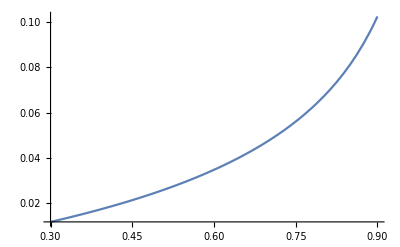

```mathematica
Plot[maxHCalcImp[180,imp,2,50],{imp,0.3,0.9},MaxRecursion->1]
```

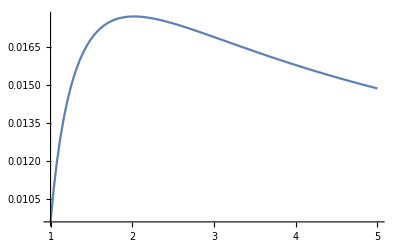

```mathematica
Plot[maxHCalcImp[180,0.4,f,50],{f,1,5},MaxRecursion->1]
```

```mathematica
f2[f_]:=maxHCalcImp[180,0.4,f,50]
```

```mathematica
FindMaximum[f2[fval], {fval,2}]
```

fval

0.4/fval

NDSolve::ndnl: Endpoint 0.4/fval in {t$79631,0.,0.4/fval} is not a real number.

NDSolve::ndsv: Cannot find starting value for the variable h$79631.

Part::partd: Part specification Domain⟦1⟧ is longer than depth of object.

Part::partd: Part specification Domain⟦2⟧ is longer than depth of object.

NDSolve::ndsv: Cannot find starting value for the variable h$79631.

Part::partd: Part specification Domain⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NDSolve::ndsv: Cannot find starting value for the variable h$79631.

General::stop: Further output of NDSolve::ndsv will be suppressed during this calculation.

NDSolve::ndsz: At t$79631 == 0.950846, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

FindMaximum::nrnum: The function value -FindMaxValue[{NDSolve[{«6»},{«3»},{«3»}]⟦1⟧⟦1⟧⟦2⟧,Domain⟦1⟧<t$79631<Domain⟦2⟧},t$79631] is not a real number at {fval} = {2.}.

FindMaximum[f2[fval],{fval,2}]

```mathematica
SetAttributes[maxHCalcImp,Listable]
```

```mathematica
Attributes[maxHCalcImp]
```

{Listable}

```mathematica
f
```

f

```mathematica
fun[x_]:=Module[{v},Print[x];v=x;Integrate[t,{t,-x,6/x}]]
```

```mathematica
FindMinimum[fun[x],x]
```

x

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{-7.8822×10^200,{x→3.97044×10^100}}

```mathematica
maxHCalcImp[180,0.4,f,50]
```

f

0.4/f

NDSolve::ndnl: Endpoint 0.4/f in {t$68587,0.,0.4/f} is not a real number.

NDSolve::ndsv: Cannot find starting value for the variable h$68587.

Part::partd: Part specification Domain⟦1⟧ is longer than depth of object.

Part::partd: Part specification Domain⟦2⟧ is longer than depth of object.

NDSolve::ndsv: Cannot find starting value for the variable h$68587.

Part::partd: Part specification Domain⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NDSolve::ndsv: Cannot find starting value for the variable h$68587.

General::stop: Further output of NDSolve::ndsv will be suppressed during this calculation.

FindMaxValue[{solc$68587⟦1⟧⟦1⟧⟦2⟧,dom$68587⟦1⟧<t$68587<dom$68587⟦2⟧},t$68587]

```mathematica
FindMaximum[{maxHCalcImp[180,m,3,50],0.1<m<0.9},{m,2},Compiled->True]
```

3

0.333333 m

NDSolve::ndnl: Endpoint 0.333333 m in {t$73607,0.,0.333333 m} is not a real number.

NDSolve::ndsv: Cannot find starting value for the variable h$73607.

Part::partd: Part specification Domain⟦1⟧ is longer than depth of object.

Part::partd: Part specification Domain⟦2⟧ is longer than depth of object.

NDSolve::ndsv: Cannot find starting value for the variable h$73607.

Part::partd: Part specification Domain⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NDSolve::ndsv: Cannot find starting value for the variable h$73607.

General::stop: Further output of NDSolve::ndsv will be suppressed during this calculation.

NDSolve::ndinnt: Initial condition Integer[0.666667] is not a number or a rectangular array of numbers.

General::stop: Further output of NDSolve::ndinnt will be suppressed during this calculation.

FindMaximum::nrnum: The function value -FindMaxValue[{NDSolve[{«6»},{«3»},{«3»}]⟦1⟧⟦1⟧⟦2⟧,Domain⟦1⟧<t$73607<Domain⟦2⟧},t$73607] is not a real number at {m} = {2.}.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

FindMaximum::nrnum: The function value -FindMaxValue[{NDSolve[{«6»},{«3»},{«3»}]⟦1⟧⟦1⟧⟦2⟧,Domain⟦1⟧<t$73607<Domain⟦2⟧},t$73607] is not a real number at {m} = {1.99999}.

FindMaximum::nrnum: The function value -FindMaxValue[{NDSolve[{«6»},{«3»},{«3»}]⟦1⟧⟦1⟧⟦2⟧,Domain⟦1⟧<t$73607<Domain⟦2⟧},t$73607] is not a real number at {m} = {0.898994}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

FindMaximum::grad: Evaluation of the gradient of function Experimental`NumericalFunction[{Hold[-FindMaxValue[{Part[«2»]⟦1⟧⟦2⟧,Domain⟦1⟧<t$73607<Domain⟦2⟧},t$73607]],Block},{0,{{{},1,0,Hold[m],0,0}}},{{{1,1,817},{«1»}}},«1»,{924,MachinePrecision,{{Automatic},{Hold[Block[{Compile`$2,Compile`$17,Compile`$45,Compile`$5,Compile`$8},«1»]],Block}},True,{«1»},FindMaximum,Automatic,None},{None,None,None}] failed at {0.899}.

FindMaximum[{maxHCalcImp[180,m,3,50],0.1<m<0.9},{m,2},Compiled→True]

```mathematica
Attributes[fun]
```

{}

```mathematica
ClearAll[f]
```

```mathematica
NArgMax[{maxHCalcImp[180,0.4,f,50],1<f<5},f]
```

f

0.4/f

NDSolve::ndnl: Endpoint 0.4/f in {t$79984,0.,0.4/f} is not a real number.

NDSolve::ndsv: Cannot find starting value for the variable h$79984.

Part::partd: Part specification Domain⟦1⟧ is longer than depth of object.

Part::partd: Part specification Domain⟦2⟧ is longer than depth of object.

NDSolve::ndsv: Cannot find starting value for the variable h$79984.

Part::partd: Part specification Domain⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NDSolve::ndsv: Cannot find starting value for the variable h$79984.

General::stop: Further output of NDSolve::ndsv will be suppressed during this calculation.

NDSolve::ndsz: At t$79984 == 1.60101, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NArgMax::nnum: The function value -FindMaxValue[{NDSolve[{Equal[«2»],Equal[«2»],Equal[«2»],Equal[«2»],Equal[«2»],Equal[«2»]},{h$79984[«1»],v$79984[«1»],m$79984[«1»]},{t$79984,Times[«2»],Times[«2»]}]⟦1⟧⟦1⟧⟦2⟧,Domain⟦1⟧<t$79984<Domain⟦2⟧},t$79984] is not a number at {f} = {1.09146}.

General::stop: Further output of NArgMax::nnum will be suppressed during this calculation.

NArgMax[{FindMaxValue[{solc$79984⟦1⟧⟦1⟧⟦2⟧,dom$79984⟦1⟧<t$79984<dom$79984⟦2⟧},t$79984],1<f<5},f]

```mathematica
Function[f, maxHCalcImp[180,0.4,f,50]]
```

Function[f,maxHCalcImp[180,0.4,f,50]]

```mathematica
Maximize[%144]
```

Maximize::argbu: Maximize called with 1 argument; between 2 and 4 arguments are expected.

Maximize[%144]

```mathematica
solb
```

solb

```mathematica
h[tsnond]== solb[[1]][[1]][[2]][[0]][tsnond]
v[tsnond]== solb[[1]][[2]][[2]][[0]][tsnond]
m[tsnond]== solb[[1]][[3]][[2]][[0]][tsnond]
```

Part::partd: Part specification solb⟦1⟧ is longer than depth of object.

Part::partd: Part specification solb⟦2⟧ is longer than depth of object.

h[tsnond]==tsnond

Part::partd: Part specification solb⟦1⟧ is longer than depth of object.

Part::partd: Part specification 1⟦2⟧ is longer than depth of object.

v[tsnond]==tsnond

Part::partd: Part specification solb⟦1⟧ is longer than depth of object.

Part::partw: Part 3 of solb⟦1⟧ does not exist.

m[tsnond]==Integer[tsnond]

```mathematica
solc
```

solc

```mathematica
FindMaxValue[{solc[[1]][[1]][[2]],dom[[1]]<t<dom[[2]]},t]
```

Part::partd: Part specification solc⟦1⟧ is longer than depth of object.

Part::partd: Part specification solc⟦2⟧ is longer than depth of object.

Part::partd: Part specification dom⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

FindMaxValue[{solc⟦1⟧⟦1⟧⟦2⟧,dom⟦1⟧<t<dom⟦2⟧},t]

```mathematica
findOptf[x_,imp_,βp_]:=Module[{interp,optf},
interp=Quiet[FunctionInterpolation[maxHCalcImp[x,imp,f,βp],{f,1,5}]];
optf=FindArgMax[{interp[f],1<f<5},{f}][[1]]]
```

```mathematica
Table[{imp,findOptf[180,imp,25]},{imp,0.2,0.9,0.1}]
```

{{0.2,3.28367},{0.3,2.29386},{0.4,1.95372},{0.5,1.74982},{0.6,1.59983},{0.7,1.47435},{0.8,1.36778},{0.9,1.27334}}

```mathematica
Table[{imp,findOptf[90,imp,25]},{imp,0.2,0.9,0.1}]
```

InterpolatingFunction::dmval: Input value {5.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {5.00003} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {5.00061} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{{0.2,4.99546},{0.3,2.77975},{0.4,2.17725},{0.5,1.88048},{0.6,1.68498},{0.7,1.53255},{0.8,1.40419},{0.9,1.29098}}

```mathematica
Table[{imp,findOptf[300,imp,25]},{imp,0.2,0.9,0.1}]
```

{{0.2,2.70683},{0.3,2.1089},{0.4,1.85908},{0.5,1.69223},{0.6,1.55972},{0.7,1.44868},{0.8,1.35144},{0.9,1.26526}}

```mathematica
%101//TableForm
```

0.2 | 2.70683
0.3 | 2.1089
0.4 | 1.85908
0.5 | 1.69223
0.6 | 1.55972
0.7 | 1.44868
0.8 | 1.35144
0.9 | 1.26526

```mathematica
1
```

```mathematica
maxHCalcImpwithPlot[x_,imp_,f_,βp_]:=
Module[{h,m,v,t,nondeqnsb,nondbcsb,nondeqnsc,nondbcsc,maxh},

tsnond = imp/f;

(*Solve boost phase*)
nondeqnsb={h'[t] == v[t],
 v'[t] == (f-x*Exp[-βp h[t]]*v[t]^2)/m[t] - 1, 
m'[t] == -f};

nondbcsb = {h[0] == 0, v[0] ==0, m[0] == 1};

solb=Evaluate[NDSolve[({nondeqnsb, nondbcsb})//Flatten,{h[t],v[t],m[t]},{t, 0.0, tsnond}]];

(*Solve coast phase*)
nondeqnsc={h'[t] == v[t],
 v'[t] == (-x*Exp[-βp h[t]]*v[t]^2)/m[t] - 1, 
m'[t] == 0};

nondbcsc = {h[tsnond]== solb[[1]][[1]][[2]][[0]][tsnond],
v[tsnond]== solb[[1]][[2]][[2]][[0]][tsnond],
m[tsnond]== solb[[1]][[3]][[2]][[0]][tsnond]};

solc=Evaluate[Quiet[NDSolve[{nondeqnsc, nondbcsc}//Flatten,{h[t],v[t],m[t]},{t,  tsnond, 20*tsnond}]]];


(*Find apogee*)
dom=solc[[1]][[1]][[2]][[0]]["Domain"][[1]];

g1=Plot[ (h[t]/.solb[[1]]),{t,0,tsnond},PlotStyle->Red];
g2=Plot[ (h[t]/.solc[[1]]),{t,dom[[1]], dom[[2]]}];

maxh=FindMaxValue[{solc[[1]][[1]][[2]],dom[[1]]<t<dom[[2]]},t]]
```

64.658

0.146148

8.8

0.00709512

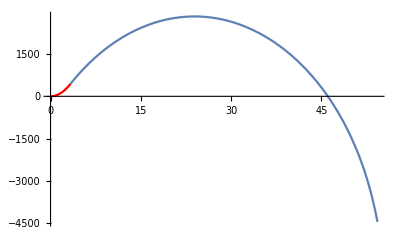

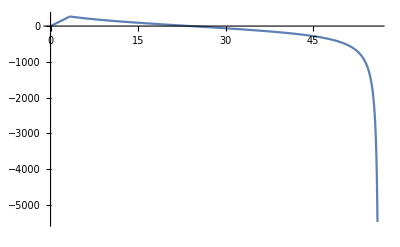

```mathematica
(*Based on McGill, Team 47 , 2018*)
x = (1/2)*1.225*2000^2*0.5*(π*(2.5*25.4/1000)^2)/(24*10)
mr = 3547/24270//N
tw =  8.8
maxHCalcImpwithPlot[x, mr,tw, 50]
g3=Plot[(c^2/g)*solb[[1]][[1]][[2]][[0]][t/(c/g)]/.{c-> 2000, g-> 10},{t, 0, tsnond*200},PlotStyle-> Red,PlotRange->All] ;
g4=Plot[(c^2/g)*solc[[1]][[1]][[2]][[0]][t/(c/g)]/.{c-> 2000, g-> 10},{t, tsnond*200,dom[[2]]*200}] ;
Show[{g3,g4},PlotRange->{0, All}]
g5=Plot[c*solb[[1]][[2]][[2]][[0]][t/(c/g)]/.{c-> 2000, g-> 10},{t, 0, tsnond*200}] ;
g6=Plot[c*solc[[1]][[2]][[2]][[0]][t/(c/g)]/.{c-> 2000, g-> 10},{t, tsnond*200,20*tsnond*200}] ;
Show[{g5,g6},PlotRange-> {0,All}]
```

34.4843

0.27972

5.7

0.0237915

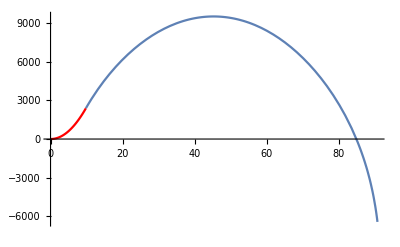

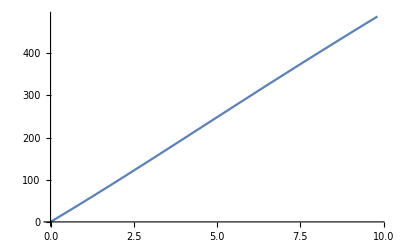

```mathematica
(*Based on Waterloo, Team 38 , 2018*)
x = (1/2)*1.225*2000^2*0.5*(π*(3*25.4/1000)^2)/(64.8*10)
mr = 40/143//N
tw = 5.7
maxHCalcImpwithPlot[x, mr,tw, 50]
g3=Plot[(c^2/g)*solb[[1]][[1]][[2]][[0]][t/(c/g)]/.{c-> 2000, g-> 10},{t, 0, tsnond*200},PlotStyle-> Red,PlotRange->All] ;
g4=Plot[(c^2/g)*solc[[1]][[1]][[2]][[0]][t/(c/g)]/.{c-> 2000, g-> 10},{t, tsnond*200,dom[[2]]*200}] ;
Show[{g3,g4},PlotRange->{0, All}]
g5=Plot[c*solb[[1]][[2]][[2]][[0]][t/(c/g)]/.{c-> 2000, g-> 10},{t, 0, tsnond*200}] ;
g6=Plot[c*solc[[1]][[2]][[2]][[0]][t/(c/g)]/.{c-> 2000, g-> 10},{t, tsnond*200,20*tsnond*200}] ;
Show[{g5,g6},PlotRange-> {0,All}]
```

83.6921

0.214286

8.5034

0.0107077

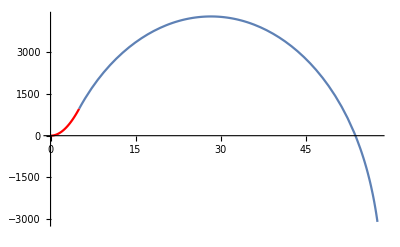

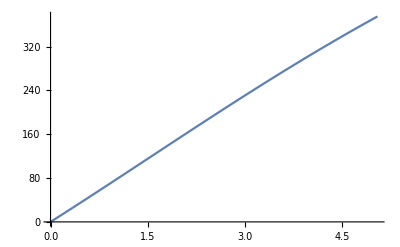

```mathematica
(*Based on UCLA, Team 108 , 2018*)
x = (1/2)*1.225*2000^2*0.5*(π*(3*25.4/1000)^2)/(26.7*10)
mr = 1-46.2/58.8//N
tw =500/58.8
maxHCalcImpwithPlot[x, mr,tw, 50]
g3=Plot[(c^2/g)*solb[[1]][[1]][[2]][[0]][t/(c/g)]/.{c-> 2000, g-> 10},{t, 0, tsnond*200},PlotStyle-> Red,PlotRange->All] ;
g4=Plot[(c^2/g)*solc[[1]][[1]][[2]][[0]][t/(c/g)]/.{c-> 2000, g-> 10},{t, tsnond*200,dom[[2]]*200}] ;
Show[{g3,g4},PlotRange->{0, All}]
g5=Plot[c*solb[[1]][[2]][[2]][[0]][t/(c/g)]/.{c-> 2000, g-> 10},{t, 0, tsnond*200}] ;
g6=Plot[c*solc[[1]][[2]][[2]][[0]][t/(c/g)]/.{c-> 2000, g-> 10},{t, tsnond*200,20*tsnond*200}] ;
Show[{g5,g6},PlotRange-> {0,All}]
```

```mathematica
π*(3*25.4/1000)^2
```

0.0182415

64.658

```mathematica
solb
solc
```

{{h$574861[t$574861]→InterpolatingFunction[{{0., 0.03}}, <>][t$574861],v$574861[t$574861]→InterpolatingFunction[{{0., 0.03}}, <>][t$574861],m$574861[t$574861]→InterpolatingFunction[{{0., 0.03}}, <>][t$574861]}}

{{h$574861[t$574861]→InterpolatingFunction[{{0.03, 0.327536}}, <>][t$574861],v$574861[t$574861]→InterpolatingFunction[{{0.03, 0.327536}}, <>][t$574861],m$574861[t$574861]→InterpolatingFunction[{{0.03, 0.327536}}, <>][t$574861]}}

0.146148

16.

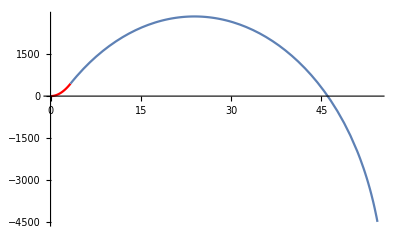

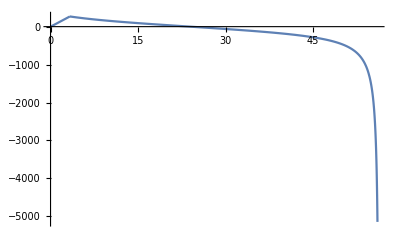

```mathematica
tsnond*200
```

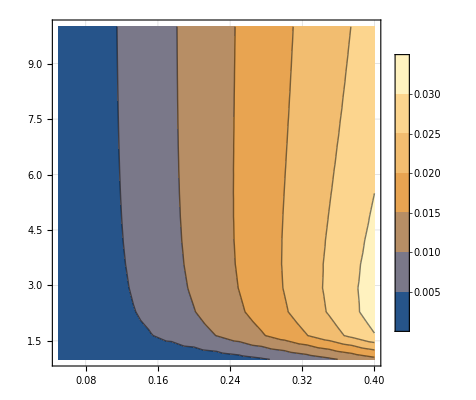

```mathematica
ContourPlot[maxHCalcImp[60, imp,f,50],{imp,0.05,0.4},{f,1,10},MaxRecursion->0,GridLines->Automatic,PlotLegends->Automatic]
```